# Learning Mathematica

## Vitor Abreu de Carvalho DRE: 121077657

## Observações

- Os comandos do Mathematica sempre começam com letras maiúsculas.

## Comandos Básicos

### Edição de Texto

- Aumentar a fonte do texto: “alt” + “=”
- Diminuir a fonte do texto: “alt” + “-“

### Codificação

Atribuição de Variáveis

```mathematica
a = 3
b = 5;
```

3

### Funções e Gráficos

```mathematica
Quit
```

## Definindo f(x)

```mathematica
f[x_]:= x^(2) ;
```

```mathematica
f[2]
```

4

```mathematica
f[4]
```

16

```mathematica
f[f[2]]
```

16

Plotagem do Gráfico da função

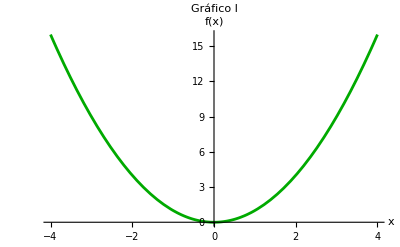

```mathematica
p1 = Plot[f[x],{x,-4,4},AxesLabel->{"x","f(x)"},PlotStyle->Darker[Green],PlotLabel->"Gráfico I"]
```

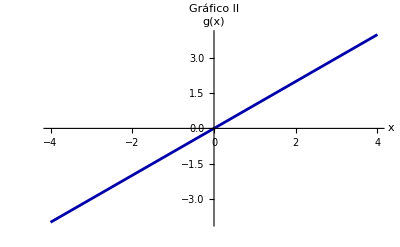

```mathematica
g[x_] := x;
p2 = Plot[g[x], {x,-4,4},AxesLabel->{"x","g(x)"},PlotStyle->Darker[Blue],PlotLabel->"Gráfico II"]
```

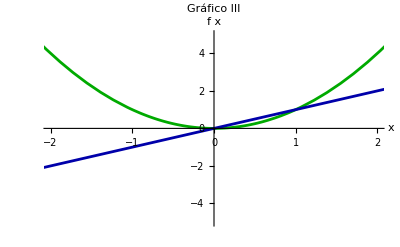

```mathematica
Show[p1,p2, PlotRange -> {{-2,2},{-5,5}}, AxesLabel -> {x, f(x)}, PlotLabel -> Gráfico III]
```

## Gráficos com parâmetros Variáveis [Manipulate]

```mathematica
Manipulate[Plot[x^(n),{x, 0,10}], {n,1,5}]
```

```mathematica
Manipulate[Plot[x^(n)+ m,{x,0,10}, PlotStyle->Darker[Green]], {n,1,5}, {m,0,5}]
```

```mathematica
Manipulate[Plot[x^(n)+ m,{x,0,10}, PlotStyle->Darker[Green], Frame-> foto], {{n,1,"Potência"},1,5}, {{m,0,"Eixo y"},0,5},{foto, {True, False}}]
```

## Listas

```mathematica
List[a,b,c]
```

{a,b,c}

```mathematica
{d,e,f,g,h}
```

{d,e,f,g,h}

```mathematica
lista = List[a,b,c]
lista1 = {d,e,f,g,h}
```

{a,b,c}

{d,e,f,g,h}

```mathematica
Length[lista1]
```

5

```mathematica
lista[[1]]
```

a

```mathematica
Append[lista1,"Vitor"]
```

```mathematica
{d,e,f,g,h,"Vitor"}
```

{d,e,f,g,h,Vitor}

```mathematica
lista1
```

{d,e,f,g,h}

```mathematica
lista3 = Append[lista1,"Vitor"]
```

{d,e,f,g,h,Vitor}

```mathematica
lista3
```

{d,e,f,g,h,Vitor}

```mathematica
lista11 = {{a,b,c},d,e,f}
```

{{a,b,c},d,e,f}

```mathematica
lista11[ [1,2] ]
```

b

```mathematica
lista11 [ [3] ]
```

e

## Tabelas